## Demonstration of a MathFEMM Analysis

David Meeker
dmeeker@ieee.org
http://femm.foster-miller.com

First, load up the MathFEMM package

```mathematica
<<c:\femm42\mathfemm\mathfemm.m
```

MathFEMM loaded at Sun 15 Nov 2015 21:02:32

The package must be initialized with the OpenFEMM[] command.  This command starts up a FEMM process and connects to it via Mathlink.

```mathematica
OpenFEMM[]
```

We need to create a new Magnetostatics document to work on.

```mathematica
NewDocument[0]
```

Define the problem type.  Magnetostatic; Units of mm; Axisymmetric; Precision of 10^(-8) for the linear solver; a placeholder of 0 for the depth dimension, and an angle constraint of 30 degrees

```mathematica
MIProbDef[0,"millimeters","axi",10^(-8),0,30]
```

Draw a rectangle for the steel bar on the axis;

```mathematica
MIDrawRectangle[{0,-40},{10,40}]
```

Draw a rectangle for the coil;

```mathematica
MIDrawRectangle[{50,-50},{100,50}]
```

Use an "Improvised Asymptotic Boundary Condition" to mimic a solution in unbounded space

```mathematica
MIMakeABC[]
```

Add block labels, one to each the steel, coil, and air regions.

```mathematica
MIAddBlockLabel[5,0]
```

```mathematica
MIAddBlockLabel[75,0]
```

```mathematica
MIAddBlockLabel[30,0]
```

Add some materials properties

```mathematica
MIAddMaterial["Air",1,1,0,0,0,0,0,1,0,0,0]
```

```mathematica
MIAddMaterial["Coil",1,1,0,0,58*0.65,0,0,1,0,0,0]
```

```mathematica
MIAddMaterial["LinearIron",2100,2100,0,0,0,0,0,1,0,0,0]
```

A more interesting material to add is the iron with a nonlinear BH curve.  First, we create a material in the same way as if we were creating a linear material, except the values used for permeability are merely placeholders.

```mathematica
MIAddMaterial["Iron",2100,2100,0,0,0,0,0,1,0,0,0]
```

A set of points defining the BH curve is then specified.

```mathematica
bhcurve=Transpose[{{0.,0.3,0.8,1.12,1.32,1.46,1.54,1.62,1.74,1.87,1.99,2.046,2.08},
{0,40,80,160,318,796,1590,3380,7960,15900,31800,55100,79600}}];
```

```mathematica
bh=Interpolation[bhcurve.{{0,1},{1,0}},InterpolationOrder->1];
```

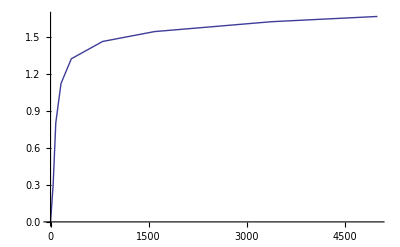

```mathematica
Plot[bh[h],{h,0,5000},PlotRange->All]
```

Another command associates this BH curve with the Iron material:

```mathematica
MIAddBHPoints["Iron",bhcurve]
```

Add a "circuit property" so that we can calculate the properties of the coil as seen from the terminals.

```mathematica
MIAddCircProp["icoil",20,1]
```

Apply the materials to the appropriate block labels

```mathematica
MISelectLabel[5,0];
MISetBlockProp["Iron",0,1,"<None>",0,0,0];
MIClearSelected[];
```

```mathematica
MISelectLabel[75,0];
MISetBlockProp["Coil",0,1,"icoil",0,0,200];
MIClearSelected[];
```

```mathematica
MISelectLabel[30,0];
MISetBlockProp["Air",0,1,"<None>",0,0,0];
MIClearSelected[];
```

Now, the finished input geometry can be displayed.

```mathematica
MIZoomNatural[]
```

```mathematica
Show[MIGetView[]]
```

-Graphics-

We have to give the geometry a name before we can analyze it.  We will save it in the examples subdirectory of MathFEMM.

```mathematica
MISaveAs[NotebookDirectory[]<>"coil.fem"]
```

Now,analyze the problem and load the solution when the analysis is finished

```mathematica
MIAnalyze[]
```

```mathematica
MILoadSolution[]
```

We can include a view of the solution's field lines in the worksheet

```mathematica
Show[MOGetView[]]
```

-Graphics-

If we were interested in the flux density at specific positions, we could inquire at specific points directly:

```mathematica
MOGetB[0,0]
```

{0,0.504426}

```mathematica
MOGetB[0,50]
```

{0,0.0547244}

Or we could, for example, plot the results along a line using Mathematica's built-in plotting routines:

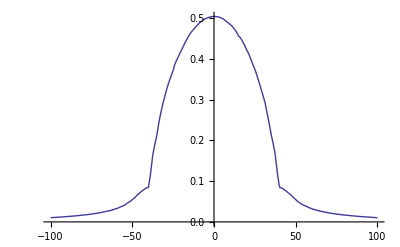

```mathematica
Plot[MOGetB[0,z]⟦2⟧,{z,-100,100},PlotPoints->10]
```

The program will report the terminal properties of the circuit:  current, voltage, and flux linkage

```mathematica
{i,v,ϕ}=MOGetCircuitProperties["icoil"]
```

{20,1.99995,0.0875335}

If we were interested in inductance, it could be obtained by dividing flux linkage by current

```mathematica
L=ϕ/i
```

0.00437668

When the analysis is completed, FEMM can be shut down.

```mathematica
CloseFEMM[]
```